```mathematica
CloseKernels[];
LaunchKernels[];
$HistoryLength=0;
ParallelEvaluate[$HistoryLength=0];
```

# Deconvolution via Approximate Maximum Likelihood

## Notation

G, K ∈ ℕ        	— Number of genes/cell types
Φ, σ ∈ ℝ_+^(G×K)  	— Matrix of single cell means/variances
Ψ ∈ ℝ_+^G 		— Bulk means
α ∈ Δ^(K-1) 		— Convex weights
n ∈ ℕ 		— Number of cells in the bulk sample
m ∈ ℕ^K 		— Number of cells  for each cell type in the single cell reference

## General Functions

mixtureσ 		— Variances of an α-mixture of distributions with means Φ and variances σ
ΦVars, αVars 	— Dummy variables used for optimization
rowℒ		— Contribution to likelihood of a single row
ℒ 			— Full Likelihood

```mathematica
mixtureσ[αList_,σRow_,ΦRow_]:=(ΦRow^2+σRow).αList-(ΦRow.αList)^2
```

```mathematica
weightedNorm[vector_,weights_,p_:2]:=Total[vector^p*weights]
```

```mathematica
mMatrix[mList_,G_]:=If[G>1,ConstantArray[mList,G],mList]
```

```mathematica
ℒ[Φ_,ΦObserved_,ΨObserved_,α_,σ_,n_,mList_]:=Total[mMatrix[mList,Length@Φ]/σ*(Φ-ΦObserved)^2,2]+Total[n/(mixtureσ[α,σ,Φ])*(Φ.α-ΨObserved/n)^2]+Total@Log[mixtureσ[α,σ,Φ]*n]
```

```mathematica
rowℒ[ΦRow_,ΦObservedRow_,ΨObservedScalar_,α_,σRow_,n_,mList_]:=Total[mList/σRow*(ΦRow-ΦObservedRow)^2]+Total[n/(mixtureσ[α,σRow,ΦRow])*(ΦRow.α-ΨObservedScalar/n)^2]+Log[mixtureσ[α,σRow,ΦRow]*n]
```

```mathematica
ΦVars[k_]:=Module[{ϕ},Array[ϕ,k]]
```

```mathematica
αVars[k_]:=Module[{α},Array[α,k]]
```

```mathematica
α=3
```

3

## Updates (1)

minΦRow 	— Optimize one row of Φ for fixed α, mixtureσ
minΦ 		— Iterate minΦRow over rows
minα 		— W-NNLS for fixed Φ, mixtureσ
minαHelper 	— Iterate minα until convergence (ε) or maxIter times
alternate 		— Alternate minΦ and minα until convergence (δ) or maxIter times

```mathematica
nUpdate[Φ_,α_,Ψ_,σ_]:=With[{G=Length@Ψ,A=weightedNorm[Φ.α,1/mixtureσ[α,σ,Φ]],C=weightedNorm[Ψ,1/mixtureσ[α,σ,Φ]]},
-G/(2A)+Sqrt[G^2/(4A^2)+C/A]]
```

```mathematica
minΦRow[ΦVars_,ΦPre_,ΨScalar_,ΦobservedRow_,σRow_,αList_,n_,mList_]:=QuadraticOptimization[Total[mList/σRow(ΦobservedRow-ΦVars)^2+n/(mixtureσ[αList,σRow,ΦPre])(ΦVars.αList-ΨScalar/n)^2],{Thread[ΦVars≥0]},ΦVars]
```

```mathematica
minΦ[ΦVars_,ΦPre_,ΨVec_,ΦMatrixObserved_,σMatrix_,αList_,n_,mList_]:=Parallelize[Table[ΦVars/.minΦRow[ΦVars,#1[[j]],#2[[j]],#3[[j]],#4[[j]],αList,n,mList]&@@{ΦPre,ΨVec,ΦMatrixObserved,σMatrix},{j,1,Length@ΨVec}]]
```

```mathematica
minα[αVars_,αPre_,σMatrix_,ΦMatrix_,ΨVector_,n_]:=αVars/.QuadraticOptimization[(n/mixtureσ[αPre,σMatrix,ΦMatrix]).(ΦMatrix.αVars-ΨVector/n)^2,Thread[αVars≥0]~Join~{Total[αVars]==1},αVars]
```

```mathematica
minαLSHelper[αVars_,αPre_,σMatrix_,ΦMatrix_,ΨVector_,n_,ε_,maxIter_]:=NestWhile[minα[αVars,#,σMatrix,ΦMatrix,ΨVector,n]&,αPre,Norm[#1-#2,2]>ε&,2,maxIter]
```

```mathematica
alternate[Φ_,Ψ_,σ_,ε_,maxIter_,δ_,mList_]:=Module[
{αNext,αPast,ΦPast,ΦNext,nPast,nNext,αList,ℒPast,ℒNext,ℒList,nList,iter=1,k=Length[First@Φ]},

ΦPast=Φ;
αPast=#/Total[#]&@(#*UnitStep[#]&/@LeastSquares[Φ,Ψ]); (* Initialise with naive least squares solution *)
nPast=Norm[#,1]&@LeastSquares[Φ,Ψ];
ℒPast=ℒ[ΦPast,Φ,Ψ,αPast,σ,nPast,mList];
ΦNext=minΦ[ΦVars[k],ΦPast,Ψ,Φ,σ,αPast,nPast,mList];
αNext=minαLSHelper[αVars[k],αPast,σ,ΦNext,Ψ,nPast,10^(-4),1];
nNext=nUpdate[ΦNext,αNext,Ψ,σ];
ℒNext=ℒ[ΦNext,Φ,Ψ,αNext,σ,nNext,mList];

αList={αPast};
ℒList={ℒPast};
nList={nPast};

Print["α_0 = ",αPast,", ℒ_0 = ",ℒPast,", n_0 = ",nPast];
Print["α = ",αNext,", ℒ = ",ℒNext,", n = ",nNext];

If[ℒNext+δ>ℒPast,αNext=αPast];

Monitor[While[Norm[αNext-αPast,Infinity]>ε&&iter<maxIter&&ℒNext+δ<ℒPast,
ΦPast=ΦNext;
αPast=αNext;
nPast=nNext;
ℒPast=ℒNext;
AppendTo[αList,αNext];
AppendTo[ℒList,ℒNext];
AppendTo[nList,nNext];
ΦNext=minΦ[ΦVars[k],ΦPast,Ψ,Φ,σ,αPast,nNext,mList];
αNext=minαLSHelper[αVars[k],αPast,σ,ΦNext,Ψ,nPast,10^(-4),1];
nNext=nUpdate[ΦNext,αNext,Ψ,σ];
ℒNext=ℒ[ΦNext,Φ,Ψ,αNext,σ,nNext,mList];
iter+=1;

Print["α = ",αNext,", ℒ = ",ℒNext,", n = ",nNext];

],iter];

{αList,ℒList,nList,ΦNext}
]
```

## Updates (2)

gradientΦRow 		— Like minΦRow, but not ignoring Φ-dependence of mixtureσ
gradientΦ 			— Iterate gradientΦRow over rows of Φ
gradientIteration 		— Alternate minα and gradientΦ until convergence (δ) or maxIter iterations

```mathematica
gradientΦRow[ΦRow_,ΦObservedRow_,ΨObservedScalar_,α_,σRow_,ΦPast_,n_,mList_]:=ΦRow/.FindMinimum[{rowℒ[ΦRow,ΦObservedRow,ΨObservedScalar,α,σRow,n,mList],Thread[ΦRow≥0]},Transpose@{ΦRow,ΦPast}][[2]]
```

```mathematica
gradientΦ[ΦVars_,ΦObserved_,ΨObserved_,α_,σ_,ΦPast_,n_,mList_]:=Parallelize[Table[gradientΦRow[ΦVars,#1[[j]],#2[[j]],α,#3[[j]],#4[[j]],n,mList]&@@{ΦObserved,ΨObserved,σ,ΦPast},{j,1,Length@σ}]]
```

```mathematica
gradientIteration[Φ_,Ψ_,ΦInit_,αInit_,nInit_,σ_,ε_,maxIter_,δ_,mList_]:=Module[
{αNext,αPast,ΦPast,ΦNext,nPast,nNext,ℒPast,ℒNext,αList,ℒList,nList,iter=1,k=Length[First@Φ]},

ΦPast=ΦInit;
αPast=αInit;
nPast=nInit;
ℒPast=ℒ[ΦPast,Φ,Ψ,αPast,σ,nPast,mList];
ΦNext=gradientΦ[ΦVars[k],Φ,Ψ,αPast,σ,ΦPast,nPast,mList];
αNext=minαLSHelper[αVars[k],αPast,σ,ΦNext,Ψ,nPast,10^(-4),1];
nNext=nUpdate[ΦNext,αNext,Ψ,σ];
ℒNext=ℒ[ΦNext,Φ,Ψ,αNext,σ,nNext,mList];

αList={αPast};
ℒList={ℒPast};
nList={nPast};

If[ℒNext+δ>ℒPast,αNext=αPast];

Print["α = ",αNext,", ℒ = ",ℒNext,", n = ",nNext];

Monitor[While[Norm[αNext-αPast,Infinity]>ε&&iter<maxIter&&ℒNext+δ<ℒPast,
ΦPast=ΦNext;
αPast=αNext;
nPast=nNext;
ℒPast=ℒNext;
AppendTo[αList,αNext];
AppendTo[ℒList,ℒNext];
AppendTo[nList,nNext];
ΦNext=gradientΦ[ΦVars[k],Φ,Ψ,αPast,σ,ΦPast,nPast,mList];
αNext=minαLSHelper[αVars[k],αPast,σ,ΦNext,Ψ,nPast,10^(-4),1];
nNext=nUpdate[ΦNext,αNext,Ψ,σ];
ℒNext=ℒ[ΦNext,Φ,Ψ,αNext,σ,nNext,mList];
iter+=1;

Print["α = ",αNext,", ℒ = ",ℒNext,", n = ",nNext];

],iter];

{αList,ℒList,nList,ΦNext}
]
```

## Hypothesis Tests

ΨTesting 			— Hypothesis testing based on residual
ΦTesting 			— Hypothesis testing based on Φ
doubleTesting 	— Combine both statistics

```mathematica
ΨTesting[Φ_,α_,Ψ_,σ_,n_]:=GammaRegularized[Length[Ψ]/2,Total[(Φ.α-Ψ/n)^2*n/mixtureσ[α,σ,Φ]]/2]
```

```mathematica
ΦTesting[Φ_,ΦObserved_,σ_,mList_]:=GammaRegularized[Times@@Dimensions[Φ]/2,Total[mMatrix[mList,Length@Φ](Φ-ΦObserved)^2/σ,2]/2]
```

```mathematica
doubleTesting[Φ_,ΦObserved_,α_,Ψ_,σ_,n_,mList_]:=GammaRegularized[(Times@@Dimensions[Φ]+Length[Ψ])/2,(Total[(Φ.α-Ψ/n)^2*n/mixtureσ[α,σ,Φ]]+Total[mMatrix[mList,Length@Φ](Φ-ΦObserved)^2/σ,2])/2]
```

## Main Function

Arguments:
	Φ, σ 			— Sample means and variances for observed single cell data
	Ψ			— Bulk sample to deconvolve
	ε, δ			— Convergence criteria for α and likelihood
	maxIter		— (Half the) Maximum number of iterations to be performed
	mList 		— Number of cells for each cell type in single cell reference
Outputs:
	αList		— List of mixture weights obtained at each iteration
	ℒList		— List of likelihoods attained at each iteration
	nList			— List of inferred n values at each iteration
     powerScores	— Outcome of the three hypothesis tests
{αLS, ℒLS, 		— Statistics as above after applying one final NNLS with updated parameters
LSpowerScores}

```mathematica
findMixtures[Φ_,Ψ_,σ_,ε_,δ_,maxIter_,mList_]:=Module[
{αListFirst,ℒListFirst,nListFirst,ΦFirst,αListSecond,ℒListSecond,nListSecond,ΦSecond,αLS,ℒLS,ℒFinal,
αListThird,ℒListThird,nListThird,ΦThird,iter=1},

{αListFirst,ℒListFirst,nListFirst,ΦFirst}=alternate[Φ,Ψ,σ,ε,maxIter,0.,mList];
{αListSecond,ℒListSecond,nListSecond,ΦSecond}=gradientIteration[Φ,Ψ,ΦFirst,αListFirst[[-1]],nListFirst[[-1]],σ,ε,maxIter,δ,mList];

αLS=Normalize[Clip[#,{0,Infinity}],Total]&@(LeastSquares[#.Φ,#.Ψ]&@DiagonalMatrix[1/Sqrt[mixtureσ[αListSecond[[-1]],σ,ΦSecond]]]);
ℒLS=ℒ[ΦSecond,Φ,Ψ,αLS,σ,nListSecond[[-1]],mList];

ℒFinal=ℒ[ΦSecond,Φ,Ψ,αListSecond[[-1]],σ,nListSecond[[-1]],mList];

Print["α_Final = ",αListSecond[[-1]],", ℒ_Final = ",ℒFinal,", n_Final = ",nListSecond[[-1]]];
Print["α_LS = ",αLS,", ℒ_LS = ",ℒLS];

While[ℒLS<ℒFinal&&iter≤maxIter,
αListSecond=αListSecond~Join~αListThird;
{αListThird,ℒListThird,nListThird,ΦThird}=gradientIteration[Φ,Ψ,ΦSecond,αLS,nListSecond[[-1]],σ,ε,maxIter,δ,mList];
αLS=Normalize[Clip[#,{0,Infinity}],Total]&@(LeastSquares[#.Φ,#.Ψ]&@DiagonalMatrix[1/Sqrt[mixtureσ[αListThird[[-1]],σ,ΦThird]]]);
ℒLS=ℒ[ΦThird,Φ,Ψ,αLS,σ,nListThird[[-1]],mList];
ℒFinal=ℒ[ΦThird,Φ,Ψ,αListThird[[-1]],σ,nListThird[[-1]],mList];
iter+=1;
Print["α_Final = ",αListThird[[-1]],", ℒ_Final = ",ℒFinal,", n_Final = ",nListThird[[-1]]];
Print["α_LS = ",αLS,", ℒ_LS = ",ℒLS];
];

{αListFirst~Join~αListSecond,ΦSecond,ℒListFirst~Join~ℒListSecond~Join~{ℒFinal},nListFirst~Join~nListSecond,{αLS,ℒLS}}
]
```

## Confidence Region

partialσ–		— ∂_x σ_g^2(α)
partial––		— ∂_(x,y) (-log ℙ)
blockMatrix	— form block-diagonal matrix with input matrices on diagonal
–MapGK		— translate indices of GK × GK matrix and its flattening

```mathematica
blockMatrix[mat_]:=SparseArray[Tuples[Range@#-{1,0,0}].{Rest@#,{1,0},{0,1}}&@Dimensions@mat->Flatten@mat]
```

```mathematica
partialσα[Φ_,σ_,α_]:=σ+Φ^2-2Φ*(Φ.α)
```

```mathematica
partialσΦ[Φ_,α_]:=2mMatrix[α,Length@Φ](Φ-Φ.α)
```

```mathematica
partialαα[Φ_,σ_,α_,n_]:=With[{σα=mixtureσ[α,σ,Φ]},
n*Transpose[Φ].DiagonalMatrix[1/σα].Φ+Transpose[partialσα[Φ,σ,α]].DiagonalMatrix[1/σα^2].partialσα[Φ,σ,α]/2
]
```

```mathematica
partialΦΦ[Φ_,σ_,α_,n_,mList_]:=With[{m=mMatrix[mList,Length@Φ],σα=mixtureσ[α,σ,Φ],αMatrix=mMatrix[α,Length@Φ],G=Length@Φ,K=Length@Φ[[1]]},
blockMatrix[ConstantArray[n*KroneckerProduct[α,α],G]/σα+(KroneckerProduct[#,#]&/@partialσΦ[Φ,α])/(2σα^2)]+DiagonalMatrix[Flatten[m/σ]]
]
```

```mathematica
partialαΦ[Φ_,σ_,α_,n_]:=With[{σα=mixtureσ[α,σ,Φ],G=Length@Φ,K=Length@α},
Table[(n*α[[Last@#]]*Φ[[First@#,k]]/σα[[First@#]]+(partialσα[Φ,σ,α][[First@#,k]]*partialσΦ[Φ,α][[First@#,Last@#]]/σα[[First@#]]^2)/2)&@backwardMapGK[index,G,K],{k,1,K},{index,1,G*K}]
]
```

```mathematica
partialnn[Φ_,σ_,α_,n_]:=With[{G=Length@Φ,σα=mixtureσ[α,σ,Φ]},
(1-G/2)/n^2+Total[(Φ.α)^2/σα]/n
]
```

```mathematica
partialnα[Φ_,σ_,α_,n_]:=With[{σα=mixtureσ[α,σ,Φ]},
Transpose[Φ/σα].(Φ.α)+Total[partialσα[Φ,σ,α]/σα]/(2n)
]
```

```mathematica
partialnΦ[Φ_,σ_,α_,n_]:=With[{σα=mixtureσ[α,σ,Φ]},
Flatten[KroneckerProduct[(Φ.α)/σα,α]+(partialσΦ[Φ,α]/σα)/(2n)]
]
```

```mathematica
forwardMapGK[g_,k_,K_]:=(g-1)*K+k
```

```mathematica
backwardMapGK[index_,G_,K_]:={Floor[(index-1)/K]+1,Mod[index-1,K]+1}
```

```mathematica
inverseFisher[Φ_,σ_,α_,n_,mList_]:=With[
{on11=partialαα[Φ,σ,α,n],on22={{partialnn[Φ,σ,α,n]}},on33=partialΦΦ[Φ,σ,α,n,mList],
off12=Transpose@{partialnα[Φ,σ,α,n]},off13=partialαΦ[Φ,σ,α,n],off23={partialnΦ[Φ,σ,α,n]}},
Part[(#+Transpose[#])/2&@Inverse[ArrayFlatten[({{on11, off12, off13}, {Transpose[off12], on22, off23}, {Transpose[off13], Transpose[off23], on33}})]],;;Length[α]+1,;;Length[α]+1]
]
```

```mathematica
crossProtocolFisherInformation[Φ_,α_,Ψ_,n_,σ_,mlist_]:=Module[{zScores=(Φ.α-Ψ/n)/(Sqrt[mixtureσ[α,σ,Φ]/n]),zTail,filterLength,filter,G=Length@Ψ},
zTail=Total[zScores^2]-G;
filterLength=Max[Ceiling[500-400Max[zTail,0]/50000],100];
filter=RandomSample[Thread[{Range[G]}],filterLength];
If[G<500,filter=Thread[{Range[G]}]];
Quiet@inverseFisher[Extract[Φ,filter],Extract[σ,filter]/.{0|0.->1.},α,n,mlist]
]
```

## Filtering

#### Filtering based on worst case distance of Ψ_g from [min Φ_g, max Φ_g] — by quantile and by absolute threshold

```mathematica
offSimplexDistances[means_,variances_,bulk_]:=With[{maxσ=Max/@variances,minμ=Min/@means,maxμ=Max/@means},
(Max/@Transpose[{Max[#,0]&/@(minμ-bulk)/maxσ,Max[#,0]&/@(bulk-maxμ)/maxσ}])
]
```

```mathematica
offSimplexFilter[Φ_,σ_,Ψ_,remainder_]:=With[{n=𝒮/.Quiet@FindMinimum[Median[offSimplexDistances[Φ,σ/𝒮,Ψ/𝒮]],{𝒮,Total[#]&@LeastSquares[Φ,Ψ]}][[2]]},
{n,Extract[#,Position[#,x_/;x≤Quantile[#,remainder/Length[#]]]&@offSimplexDistances[Φ,σ/n,Ψ/n]]&/@{Φ,σ,Ψ}}
]
```

```mathematica
offSimplexFilterAbsolute[Φ_,σ_,Ψ_,p_]:=With[{n=𝒮/.Quiet@FindMinimum[{Median[offSimplexDistances[Φ,σ/𝒮,Ψ/𝒮]],𝒮>0},{𝒮,Total[#]&@LeastSquares[Φ,Ψ]}][[2]]},
{n,Extract[#,Position[#,x_/;x≤p]&@offSimplexDistances[Φ,σ/n,Ψ/n]]&/@{Φ,σ,Ψ}}
]
```

```mathematica
adjustVariances[Φ_,σ_,Ψ_,p_]:=With[{n=𝒮/.Quiet@FindMinimum[{Median[offSimplexDistances[Φ,σ/𝒮,Ψ/𝒮]],𝒮>0},{𝒮,Total[#]&@LeastSquares[Φ,Ψ]}][[2]]},
p*σ*(offSimplexDistances[Φ,σ/n,Ψ/n]/.{0|0.->1.})
]
```

```mathematica
simpleFilter[Φ_,Ψ_]:=With[{nonzeroΦ=Position[Max/@Φ,x_/;x>0],nonzeroΨ=Position[Ψ,x_/;x>0]},Intersection[nonzeroΦ,nonzeroΨ]]
```

#### Empirical Protocol Filters

Filter a gene g based on its (one-sided) distance (in units of median deviations) from the median of the following key statistics:
	
	1. max {(σ_(g,k)^2)/(Φ_(g,k))}_(k∈[K])
	2. min {Ψ_g/(Φ_(g,k))}_(k∈[K])

Individual thresholds (given by thresholdrule and iterationrule) are based on empirical trends in thirteen tissues of the Tabula Muris dataset

• F/D Filtering Helper Functions

```mathematica
fdfilter[Φ_,σ_,Ψ_,mdplus_:0,mdminus_:Infinity,extraratio_:0]:=With[{
σΦratios=Max/@(σ/(Φ/.{0|0.->10^(-10)})),
ΨΦratios=Min/@(Ψ/(Φ/.{0|0.->10^(-10)})),
nonzeros=Position[Max/@Φ,x_/;x>0.],
Φm=Median[Max/@Φ],Φmd=MedianDeviation[Max/@Φ],
σm=Median[Max/@σ],σmd=MedianDeviation[Max/@σ],
σΦm=Median[Max/@(σ/(Φ/.{0|0.->10^(-10)}))],σΦmd=MedianDeviation[Max/@(σ/(Φ/.{0|0.->10^(-10)}))],
ΨΦm=Median[Min/@(Ψ/(Φ/.{0|0.->10^(-10)}))],ΨΦmd=MedianDeviation[Min/@(Ψ/(Φ/.{0|0.->10^(-10)}))]
},

Intersection[
nonzeros,
Position[Ψ,x_/;x>0.],
Position[Max/@Φ,x_/;Φm-Φmd*mdminus≤x≤Φm+Φmd*mdplus],
Position[Max/@σ,x_/;σm-σmd*mdminus≤x≤σm+σmd*mdplus],
Position[σΦratios,x_/;σΦm-σΦmd*mdminus≤x≤σΦm+σΦmd*mdplus],
Position[ΨΦratios,x_/;ΨΦm-ΨΦmd*Infinity≤x≤ΨΦm+ΨΦmd*mdplus]
]
]
```

```mathematica
fdthresholdrule[Φ_,σ_,Ψ_]:=With[{
ΨΦratios=Min/@Extract[Ψ/(Φ/.{0|0.->10^(-10)}),Intersection[Position[Max/@Φ,_?Positive],Position[Ψ,_?Positive]]]},
If[(MedianDeviation[#]/Median[#]<0.55)&&(Skewness[#]<105),1,5]&@ΨΦratios
]
```

```mathematica
fditerationrule[Φ_,σ_,Ψ_]:=With[{
ΨΦratios=Min/@Extract[Ψ/(Φ/.{0|0.->10^(-10)}),Intersection[Position[Max/@Φ,_?Positive],Position[Ψ,_?Positive]]]},
If[(0.52<MedianDeviation[#]/Median[#]<0.7)||(.06<Quantile[#,0.05]/Median[#]<0.18),1,2]&@ΨΦratios
]
```

• Final F/D Filtering (note: iterations is to be fed as maxIter into findMixture)

```mathematica
filterFD[Φ_,σ_,Ψ_]:=With[{threshold=fdthresholdrule[Φ,σ,Ψ],iterations=fditerationrule[Φ,σ,Ψ]},
{iterations,fdfilter[Φ,σ,Ψ,threshold,3]}
]
```

• D/F Filtering Helper Functions

```mathematica
dffilter[Φ_,σ_,Ψ_,mdplus_:0,mdminus_:Infinity]:=With[{
σΦratios=Max/@(σ/(Φ/.{0|0.->10^(-10)})),
ΨΦratios=Min/@(Ψ/(Φ/.{0|0.->10^(-10)})),
nonzeros=Position[Max/@Φ,x_/;x>0.],
Φm=Median[Max/@Φ],Φmd=MedianDeviation[Max/@Φ],
σm=Median[Max/@σ],σmd=MedianDeviation[Max/@σ],
σΦm=Median[Max/@(σ/(Φ/.{0|0.->10^(-10)}))],σΦmd=MedianDeviation[Max/@(σ/(Φ/.{0|0.->10^(-10)}))],
ΨΦm=Median[Min/@(Ψ/(Φ/.{0|0.->10^(-10)}))],ΨΦmd=MedianDeviation[Min/@(Ψ/(Φ/.{0|0.->10^(-10)}))]
},

Intersection[
nonzeros,
Position[Ψ,x_/;x>0.],
Position[Max/@Φ,x_/;Φm-Φmd*mdminus≤x≤Φm+Φmd*mdplus],
Position[Max/@σ,x_/;σm-σmd*mdminus≤x≤σm+σmd*mdplus],
Position[σΦratios,x_/;σΦm-σΦmd*mdminus≤x≤σΦm+σΦmd*mdplus],
Position[ΨΦratios,x_/;ΨΦm-ΨΦmd*mdminus≤x≤ΨΦm+ΨΦmd*mdplus]
]
]
```

```mathematica
dfiterationrule[Φ_,σ_,Ψ_]:=With[{
leftTail=Quantile[#,0.05]/Median[#]&@(Min/@Extract[Ψ/(Φ/.{0|0.->10^(-10)}),Intersection[Position[Max/@Φ,_?Positive],Position[Ψ,_?Positive]]])},

If[leftTail≥0.1,1,3]
]
```

```mathematica
dfthresholdrule[Φ_,σ_,Ψ_]:=With[{
skew=Skewness[Max/@Extract[σ/(Φ/.{0|0.->10^(-10)}),Intersection[Position[Max/@Φ,_?Positive],Position[Ψ,_?Positive]]]]
},

If[skew≤40,4,If[skew≤60,1,7]]
]
```

• Final D/F Filtering (note: iterations is to be fed as maxIter into findMixture; moreover, final projection typically outperform the minimizer resulting from the alternating optimization, so should be selected by default)

```mathematica
filterDF[Φ_,σ_,Ψ_]:=With[{threshold=dfthresholdrule[Φ,σ,Ψ],iterations=dfiterationrule[Φ,σ,Ψ]},
{iterations,dffilter[Φ,σ,Ψ,threshold,Infinity]}
]
```

## Example Run

```mathematica
g=1000;
(*k=4;*)
k=4;
mList=ConstantArray[200.,k];
ϕ=RandomVariate[ExponentialDistribution[1/100],{g,k}];
σ=10ϕ;
(*α={6,4,3,3}/16.;*)
α={4,3,2,1}/10.;
n=500.;ψ=n*ϕ.α;
```

```mathematica
Φ=ϕ+Table[RandomVariate[NormalDistribution[0,σ[[i,j]]/mList[[j]]]],{i,1,Length@ϕ},{j,1,Length@α}];Ψ=ψ+(RandomVariate[NormalDistribution[0,Sqrt[#]]]&/@(n*mixtureσ[α,σ,ϕ]));
```

```mathematica
Quiet[{αInferred,ℒInferred,nInferred,LSInferred}=findMixtures[Φ,Ψ,σ,10^(-10),10^(-10),3,mList]];
```

α_0 = {0.400573,0.302773,0.198968,0.0976865}, ℒ_0 = 16609.2, n_0 = 501.03

α = {0.401392,0.301756,0.199124,0.0977281}, ℒ = 17034.4, n = 500.762

α = {0.40188,0.301099,0.19905,0.0979709}, ℒ = 16241.1, n = 500.858

α = {0.402051,0.300899,0.199049,0.0980007}, ℒ = 16240.7, n = 500.828

α = {0.402073,0.300877,0.199047,0.0980034}, ℒ = 16240.7, n = 500.822

α_Final = {0.402051,0.300899,0.199049,0.0980007}, ℒ_Final = 16240.7, n_Final = 500.828

α_LS = {0.401982,0.300677,0.199016,0.0983248}, ℒ_LS = 16240.8

```mathematica
ℒ[ϕ,ϕ,ψ,α,σ,n,mList]
```

14586.6

```mathematica
100Mean@Abs[α-αInferred[[-1]]]
```

0.147521

```mathematica
fisherInverse=inverseFisher[Φ,σ,α,n,mList];
```

```mathematica
{#,CDF[ChiSquareDistribution[k],#]}&@((α-αInferred[[-1]]).Inverse[fisherInverse[[;;k,;;k]]].(α-αInferred[[-1]]))
```

{4.98721,0.711387}

### L_1 errors between estimation and truth (in percent per cell type)

```mathematica
((Norm[#,1]/Length[α]&/@(αInferred-ConstantArray[α,Length@αInferred]))~Join~{Norm[LSInferred[[1]]-α,1]})*100
```

{0.205117,0.149154,0.108258,0.108258,0.0782672,0.0743096,0.109075,0.0844002,0.0786218,0.109075,0.0844002,0.0786218,0.109082,0.0844021,0.0786223,0.218165}

```mathematica
Quiet[{αTest,ΦTest,nTest,LSTest}=findMixturesFull[Φ,Ψ,σ,10^(-10),10^(-10),3,mList]];
```

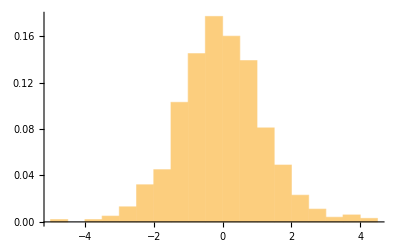

```mathematica
Histogram[(ΦTest.αTest[[-1]]-Ψ/nTest[[-1]])/(Sqrt[mixtureσ[αTest[[-1]],σ,ΦTest]/nTest[[-1]]]),{0.5},"Probability",PlotRange->All]
```